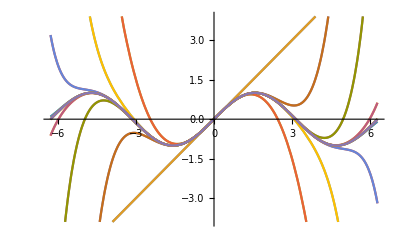

```mathematica
Plot[Evaluate[Table[Normal[Series[Sin[x],{x,0,n}]],{n,20}]],{x,-2Pi,2Pi}]
```

```mathematica
Manipulate[Plot[{Sin[x],Evaluate[Table[Normal[Series[Sin[x],{x,0,m}]],{m,n}]]},{x,-2Pi,2Pi},Filling->{1->{n}},PlotRange->3,AspectRatio->Automatic],{n,1,20,1}]
```

```mathematica
Manipulate[Plot[{Evaluate[FourierTrigSeries[π/4Sign[x],x,n]],π/4Sign[Mod [(x+π),2π]-π]},{x,-2π,2π},PlotRange->1,AspectRatio->Automatic],{n,1,20,1}]
```